```mathematica
my指数分布=ExponentialDistribution[1/8000]
```

ExponentialDistribution[1/8000]

```mathematica
PDF[my指数分布] (*获得"概率函数"*)
```

Function[x,Piecewise[{{ⅇ^(-x/8000)/8000, x≥0}, {0, True}}],Listable]

```mathematica
CDF[my指数分布](*获得"累加函数"*)
```

Function[x,Piecewise[{{1-ⅇ^(-x/8000), x≥0}, {0, True}}],Listable]

```mathematica
CDF[my指数分布,5000]
```

(在x=5000处的 累加函数F(x)值=0.46)

1-1/ⅇ^(5/8)

```mathematica
N[1-1/ⅇ^(5/8)]
```

0.464739

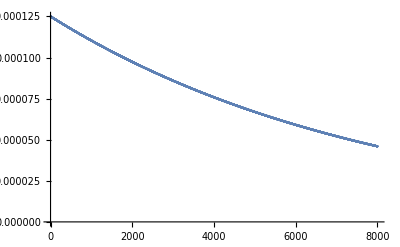

```mathematica
ListPlot[Table[PDF[my指数分布,x],{x,0,8000}],
PlotLegends->"PDF=ⅇ^(-x/8000)/8000"]
```

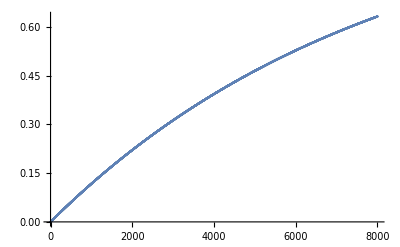

```mathematica
ListPlot[Table[CDF[my指数分布,x],{x,0,8000}],
PlotLegends->"CDF=1-ⅇ^(-x/8000)"]
```

```mathematica
list={26,33,65,28,34,55,25,44,50,36,26,37,43,62,35,38,45,32,28,34} \\
```

第1步: 先算”正态分布”所需要的两个参数: 均值μ, 标准差σ

```mathematica
res均值=Mean[list]
```

194/5

```mathematica
N[res均值]
```

38.8

```mathematica
res标准差=StandardDeviation[list]
```

6 √(19/5)

```mathematica
N[res标准差]
```

11.6962

```mathematica
res正态分布= NormalDistribution[res均值,res标准差]
```

NormalDistribution[194/5,6 √(19/5)]

```mathematica
https://jingyan.baidu.com/article/08b6a591958d5b14a8092284.html
```